# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Channels

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Channels\\packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Channels\\packages\\Chaometer.wl"]
```

# Interacting two qubits

```mathematica
PauliMatrix[0]//MatrixForm
PauliMatrix[1]//MatrixForm
PauliMatrix[2]//MatrixForm
PauliMatrix[3]//MatrixForm
```

(1 | 0
0 | 1)

(0 | 1
1 | 0)

(0 | -ⅈ
ⅈ | 0)

(1 | 0
0 | -1)

```mathematica
Clear[ham];
ham[a_]:=(KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]])+(KroneckerProduct[PauliMatrix[0],PauliMatrix[1],PauliMatrix[0]]+KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[1]])+c*(KroneckerProduct[PauliMatrix[1],PauliMatrix[1],PauliMatrix[0]])
```

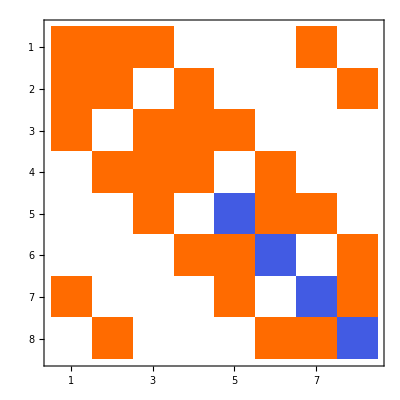

```mathematica
ham[1]//MatrixPlot
```

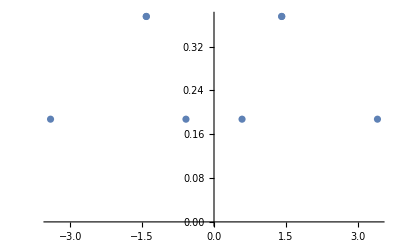

```mathematica
a=1;
b=1;
c=1;
h=ham[c];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[h]]]]];
iprs=Table[Total[Total[Abs[i]^4]],{i,eigenvec}];
ListPlot[Transpose[{eigenval,iprs}]]
```

```mathematica
Clear[u];
u[t_]:=MatrixExp[-I*t*h];
```

```mathematica
evol5=Table[u[t].Flatten[KroneckerProduct[{1,0},{1,0},Normalize[{RandomReal[],RandomReal[]}]]],{t,0,10,0.05}];
tlist=Range[0,10,0.05];
sp5=Table[{tlist[[i]],Abs[Conjugate[evol5[[1]]].evol5[[i]]]^2},{i,Length[evol1]}];
```

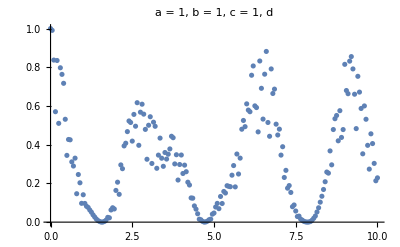

```mathematica
ListPlot[sp5,PlotRange->All,PlotLegends->Automatic,PlotLabel->Style["a = "<>ToString[a]<>", b = "<>ToString[b]<>", c = "<>ToString[c]<>", d",20,Black]]
```

## Channels

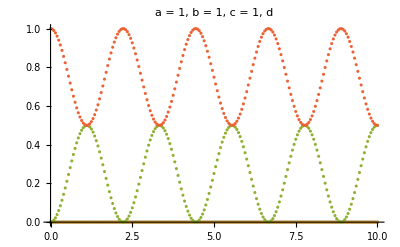

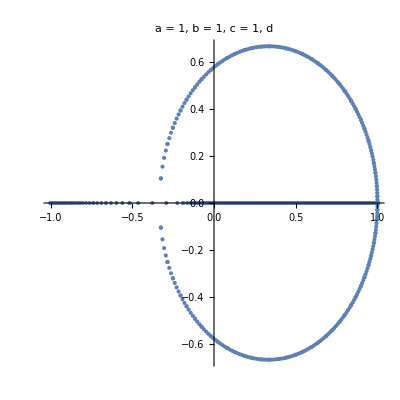

```mathematica
ψe={1,0,0,0};
choival=Table[Transpose[{ConstantArray[t,4],Sort[Chop[Eigenvalues[(1/2)Reshuffle[Superoperator[t,ψe,eigenval,eigenvec,3]]]]]}],{t,tlist}];
ListPlot[Transpose[choival],PlotRange->All,PlotLabel->Style["a = "<>ToString[a]<>", b = "<>ToString[b]<>", c = "<>ToString[c]<>", d",20,Black]]
supval=Table[Eigenvalues[Superoperator[t,ψe,eigenval,eigenvec,3]],{t,tlist}];
ComplexListPlot[Flatten[supval],PlotRange->All,AspectRatio->1,PlotLabel->Style["a = "<>ToString[a]<>", b = "<>ToString[b]<>", c = "<>ToString[c]<>", d",20,Black]]
```

```mathematica
ψe={0,0,0,1};
choival=Table[Transpose[{ConstantArray[t,4],Sort[Chop[Eigenvalues[(1/2)Reshuffle[Superoperator[t,ψe,eigenval,eigenvec,3]]]]]}],{t,tlist}];
ListPlot[Transpose[choival],PlotRange->All,PlotLabel->Style["a = "<>ToString[a]<>", b = "<>ToString[b]<>", c = "<>ToString[c]<>", d",20,Black]]
supval=Table[Eigenvalues[Superoperator[t,ψe,eigenval,eigenvec,3]],{t,tlist}];
ComplexListPlot[Flatten[supval],PlotRange->All,AspectRatio->1,PlotLabel->Style["a = "<>ToString[a]<>", b = "<>ToString[b]<>", c = "<>ToString[c]<>", d",20,Black]]
```

-Graphics-

-Graphics-

```mathematica
ψe=Flatten[KroneckerProduct[{1,0},Normalize[{RandomReal[],Exp[I*RandomReal[]]*RandomReal[]}]]];
choival=Table[Transpose[{ConstantArray[t,4],Sort[Chop[Eigenvalues[(1/2)Reshuffle[Superoperator[t,ψe,eigenval,eigenvec,3]]]]]}],{t,tlist}];
ListPlot[Transpose[choival],PlotRange->All,PlotLabel->Style["a = "<>ToString[a]<>", b = "<>ToString[b]<>", c = "<>ToString[c]<>", d",20,Black]]
supval=Table[Eigenvalues[Superoperator[t,ψe,eigenval,eigenvec,3]],{t,tlist}];
ComplexListPlot[Flatten[supval],PlotRange->All,AspectRatio->1,PlotLabel->Style["a = "<>ToString[a]<>", b = "<>ToString[b]<>", c = "<>ToString[c]<>", d",20,Black]]
```

-Graphics-

-Graphics-